# Functions

# Work

## 1. One Point, One Dimension

```mathematica
Random[]
```

0.964906

```mathematica
Random[]&/@Range[20]
```

{0.730696,0.0674141,0.495873,0.530105,0.413933,0.949673,0.736767,0.178188,0.321189,0.873777,0.498283,0.862257,0.128748,0.438067,0.718791,0.413477,0.954773,0.494379,0.086418,0.0202353}

```mathematica
Mean[Random[]&/@Range[10000]]
```

0.500804

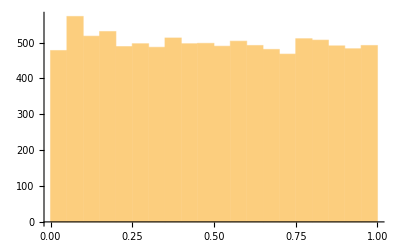

```mathematica
Histogram[Random[]&/@Range[10000]]
```

## 2. Two Points, One Dimension

```mathematica
data={};
For[i=1, i<100000,
pointA=Random[];
pointB=Random[];
value=Abs[pointA-pointB];
data = Append[data, value];
i++]
```

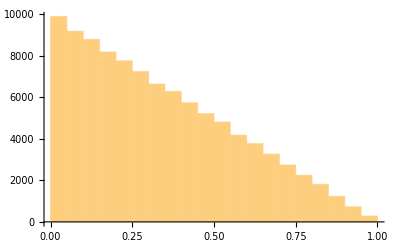

```mathematica
Histogram[data]
```

```mathematica
Mean[data]
```

0.333238

```mathematica
(* Is it intuitive that two random points split the segment into thirds?*)
```

```mathematica
(* What do you expect to happen if the boundary conditions are c*)
```

```mathematica
data1b={};
For[i=1, i<10000,
pointA=Random[];
pointB=Random[];
points=Sort[{pointA, pointB}, #1 < #2 &];
value1b=Min[{Abs[points[[1]]+1-points[[2]]], points[[2]]-points[[1]]}];
data1b = Append[data1b, value1b];
i++];
```

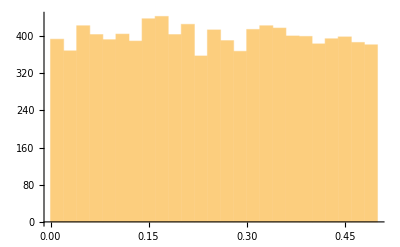

```mathematica
Histogram[data1b]
```

```mathematica
Mean[data1b]
```

0.248814

## 3. 3 points, One dimension

```mathematica
data1={};
data2={};
data3={};
For[i=1, i<10000,
pointA=Random[];
pointB=Random[];
pointC=Random[];
points = Sort[{pointA, pointB, pointC}, #1<#2 &];
value1=Abs[points[[3]]-points[[2]]];
value2=Abs[points[[2]]-points[[1]]];
value3=Abs[points[[3]]-points[[1]]];
data1 = Append[data1, value1];
data2 = Append[data2, value2];
data3 = Append[data3, value3];
i++]
```

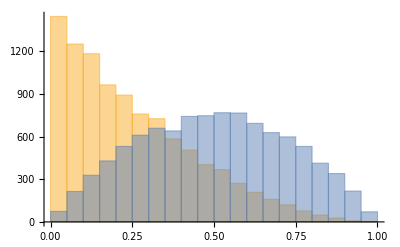

```mathematica
Histogram[{data1, data3}]
```

```mathematica
Mean[#]&/@{data1,data2,  data3}
```

{0.251742,0.24807,0.499812}

```mathematica
(* Is it obvious that 3 points split the segment into quarters? *)
```

```mathematica
(* These three examples are the foundation for the rest of the book.We will explore more complex geometries,higher dimensions and different constraints but fundamentally we will explore how randomness (and patterns) are influenced by geometry. *)
```

## 4. Two Points on a Circle

```mathematica
data={};
thetaData={};
For[i=1, i<10000,
pointA=generateRandomPointOnCircle[1];
pointB=generateRandomPointOnCircle[1];
value=computeDistance[pointA[[1;;2]], pointB[[1;;2]]];
data = Append[data, value];
thetaDelta = Abs[pointA[[3]]-pointB[[3]]];
thetaData=Append[thetaData, If[thetaDelta > Pi, 2*Pi - thetaDelta, thetaDelta]];
i++];
```

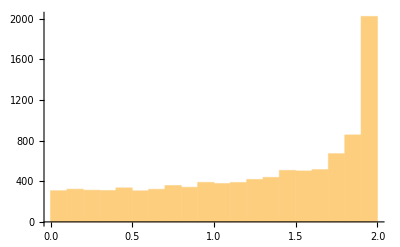

```mathematica
Histogram[data]
```

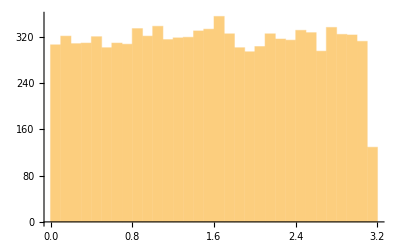

```mathematica
Histogram[thetaData]
```

```mathematica
(* Given theta is equal everwhere, there is a high probability of the other point being on the other side of the circle. *)
```

```mathematica
{Mean[data],N[4/Pi], Mean[thetaData], N[2*Pi/4]}
```

{1.27748,1.27324,1.5756,1.5708}

```mathematica
(* What if we fix a point on the circle, what do you think would happen? 

*)
```

```mathematica
data={};
thetaData={};
For[i=1, i<10000,
pointA={1, 0, 0};
pointB=generateRandomPointOnCircle[1];
value=computeDistance[pointA[[1;;2]], pointB[[1;;2]]];
data = Append[data, value];
thetaDelta = Abs[pointA[[3]]-pointB[[3]]];
thetaData=Append[thetaData, If[thetaDelta > Pi, 2*Pi - thetaDelta, thetaDelta]];
i++];
```

```mathematica
(* I expected them to be the same but still am surprised. *)
```

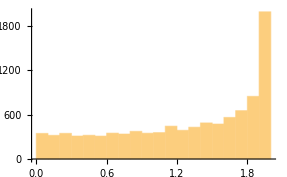
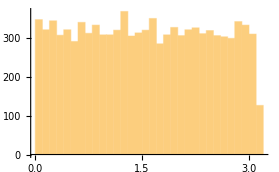

```mathematica
{Histogram[data], Histogram[thetaData]}
```

## 5. Two Points in Two Dimensions

### Square

```mathematica
data={};
For[i=1, i<100000,
pointA=Random[]&/@Range[2];
pointB=Random[]&/@Range[2];
value=computeDistance[pointA, pointB];
data = Append[data, value];
i++]
```

```mathematica
Mean[data]
```

0.52115

```mathematica
N[(2+Sqrt[2]+5 *Log[Sqrt[2]+1])/15]
```

0.521405

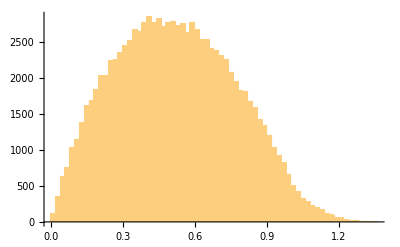

```mathematica
Histogram[data, 50]
```

### Circle

```mathematica
data={};
For[i=1, i<100000,
pointA=throwRandomPointInCircle[1/Sqrt[Pi]];
pointB=throwRandomPointInCircle[1/Sqrt[Pi]];
value=computeDistance[pointA, pointB];
data = Append[data, value];
i++]
```

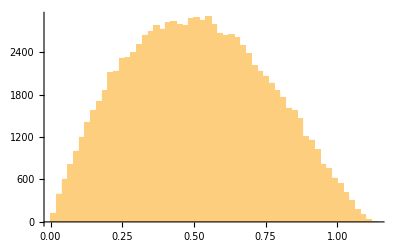

```mathematica
Histogram[data, 50]
```

```mathematica
Mean[data]
```

0.511004

```mathematica
(* So this is slightly smaller than the square by less than 3%.  My new idea is that while the maximum distance in a square is Sqrt(2)= 1.41, the maximum distance in a circle is only 2/Sqrt[Pi] = 1.12.  What do we expect for a triangle of the same area?  An equilateral triangle with an area of 1 will have a side length and max distance of 2/Sqrt[3]=1.15 so might expect it to have a higher average distance. *)
```

### Triangle

```mathematica
data={};
For[i=1, i<100000,
pointA=throwRandomPointInTriangle[];
pointB=throwRandomPointInTriangle[];
value=computeDistance[pointA, pointB];
data = Append[data, value];
i++]
```

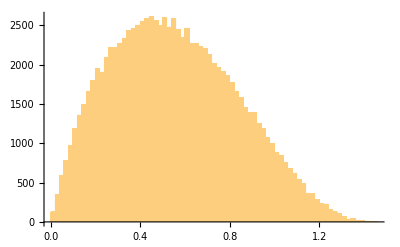

```mathematica
Histogram[data, 50]
```

```mathematica
Mean[data]
```

0.554826

```mathematica
(* So the average distance in a triangle is actually greater than in a square by almost 6%.  I'm suspecting this is due to the fact that we have two options for the long distance (either other corner, as opposed to just on option in the square. )*)
```

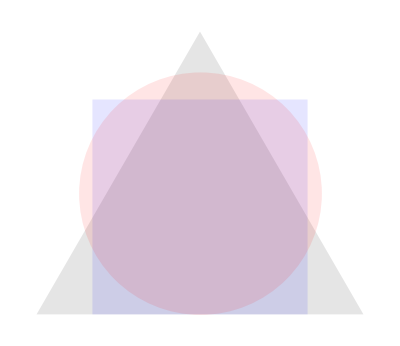

```mathematica
Graphics[{Opacity[0.1],Triangle[{{1/3^(1/4), 0}, {0, 3^(1/4)}, {-1/3^(1/4), 0}}], Blue, Polygon[{{-0.5, 0}, {-0.5, 1}, {0.5, 1}, {0.5, 0}}], Red, Disk[{0, 1/Sqrt[Pi]}, 1/Sqrt[Pi]] }]
```

### Distance From Center

## 6. Distance from the Center

```mathematica
data={};
For[i=1, i<100000,
pointA=Random[]&/@Range[2];
pointB={0.5, 0.5};
value=computeDistance[pointA, pointB];
data = Append[data, value];
i++]
```

```mathematica
Mean[data]
```

0.38231

```mathematica
data={};
For[i=1, i<100000,
pointA=throwRandomPointInCircle[1/Sqrt[Pi]];
pointB={0,0};
value=computeDistance[pointA, pointB];
data = Append[data, value];
i++]
```

```mathematica
Mean[data]
```

0.376288

```mathematica
data={};
For[i=1, i<100000,
pointA=throwRandomPointInTriangle[];
pointB={0, 1/Sqrt[3]};
value=computeDistance[pointA, pointB];
data = Append[data, value];
i++];
Mean[data]
```

0.420717

## 7. Two Points, Large Dimensionality

```mathematica
dataSet={};
For[dim=1, dim<30, 
data={};
n=20000;
For[i=1, i<n,
pointA=Random[]&/@Range[dim];
pointB=Random[]&/@Range[dim];
value=computeDistance[pointA, pointB];
data = Append[data, value];
i++];
dataSet=Append[dataSet, data]; (* Sqrt[dim] is the longest possible distance length along diagonal of hypercube  *)
dim++]
```

```mathematica
Mean[#]&/@dataSet
```

{0.332336,0.369618,0.382366,0.38732,0.392292,0.394571,0.396645,0.398718,0.400488,0.400693,0.402298,0.401698,0.402329,0.403524,0.403721,0.403666,0.403724,0.404785,0.404421,0.405656,0.404871,0.40538,0.405433,0.404839,0.405879,0.406041,0.404881,0.406121,0.406386}

```mathematica
(* Need generatae histogram here.
computeHistogram[data_, min_, max_, binCount_]
 *)
```

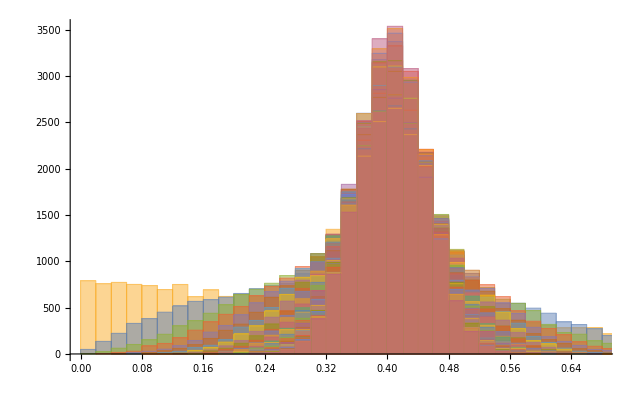

```mathematica
Histogram[#&/@dataSet, 50]
```

```mathematica
(* I don't think I hsve found any good evidence on the web yet about where this number 0.405 comes from...*)
```

## 8. Three Points, 2 Dimensions, Square

```mathematica
dataSetMin={};
dataSetMax={};
dataSet = {};
For[dim=1, dim<21, 
dataMin={};
dataMax={};
n=1000;
For[i=1, i<n,
pointA=Random[]&/@Range[dim];
pointB=Random[]&/@Range[dim];
pointC=Random[]&/@Range[dim];
value1=computeDistance[pointA, pointB];
value2=computeDistance[pointA, pointC];
value3=computeDistance[pointC, pointB];
values={value1, value2, value3};
dataMin = Append[dataMin, Min[values]];
dataMax = Append[dataMax, Max[values]];
dataSet=Append[dataSet, Mean[values]];
i++];
dataSetMin=Append[dataSetMin, dataMin/Sqrt[dim]];
dataSetMax=Append[dataSetMax, dataMax/Sqrt[dim]];
dataSet=Append[dataSet, dataSet/Sqrt[dim]];
dim++]
```

```mathematica
(* This plot shows the average smallest side of a triangle and the average longest side as a function of N dimensions. *)
```

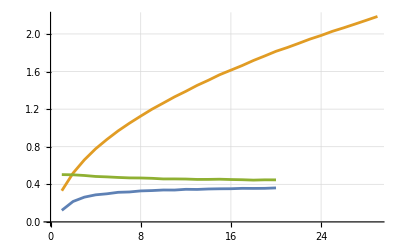

```mathematica
ListPlot[{Mean[#]&/@dataSetMin, Mean[#]&/@dataSet, Mean[#]&/@dataSetMax}, Joined -> True, GridLines->Automatic]
```

## 9. Intersecting Lines

```mathematica
dataSet={};
n=10000;
For[i=1, i<n,
lineA={{Random[], Random[]}, {Random[], Random[]}};
lineB={{Random[], Random[]}, {Random[], Random[]}};
mA=(lineA[[1]][[2]]-lineA[[2]][[2]])/(lineA[[1]][[1]]-lineA[[2]][[1]]);
bA = lineA[[1]][[2]]-mA*lineA[[1]][[1]];
mB=(lineB[[1]][[2]]-lineB[[2]][[2]])/(lineB[[1]][[1]]-lineB[[2]][[1]]);
bB = lineB[[1]][[2]]-mB*lineB[[1]][[1]];
xInt = (bA-bB)/(mB-mA);
yIntp = mA*xInt+bA;
(* Replace this with chechCrosses[pin] *)
dataSet = Append[dataSet, If[xInt < 1 && xInt > 0 && yIntp < 1 && yIntp > 0, 1, 0]];
i++];
```

```mathematica
(* The histogram is binary here so it is not as interesting :) *)
```

```mathematica
N[Total[dataSet]/10000]
```

0.6869

```mathematica
(* In this case we generated random points in a region that subsequently  made random lines.  But what if we add a further constraint that we want the line to be of a certain length (L < 1).  We'll need some new code for that :)*)
```

```mathematica
data={};
For[j=1, j < 13, (* Want to replace with j<14 (14 would be the actual contraint but long run time?  I wonder if at this point in which there is strong correlation with the diagonal the probability drops more  *)
dataSet={};
n=1000;
For[i=1, i<n,
lineA=getPinFit[j/10];
lineB=getPinFit[j/10];
mA=(lineA[[1]][[2]]-lineA[[2]][[2]])/(lineA[[1]][[1]]-lineA[[2]][[1]]);
bA = lineA[[1]][[2]]-mA*lineA[[1]][[1]];
mB=(lineB[[1]][[2]]-lineB[[2]][[2]])/(lineB[[1]][[1]]-lineB[[2]][[1]]);
bB = lineB[[1]][[2]]-mB*lineB[[1]][[1]];
xInt = (bA-bB)/(mB-mA);
yIntp = mA*xInt+bA;
(* We dont yet check here whether the crosses are on the line segment itself! *)
dataSet = Append[dataSet, If[xInt < 1 && xInt > 0 && xInt<Max[lineA[[1]][[1]], lineA[[2]][[1]]] && xInt>Min[lineA[[1]][[1]], lineA[[2]][[1]]] && yIntp < 1 && yIntp > 0 && yIntp<Max[lineA[[1]][[2]], lineA[[2]][[2]]] && yIntp>Min[lineA[[1]][[2]], lineA[[2]][[2]]], 1, 0]];
i++];
data = Append[data,{N[j/10], N[Total[dataSet]/1000]}];
j++]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit::reclim will be suppressed during this calculation.

$Aborted

```mathematica
(* We hit a recursion limit when the pin length hits 1.2 and must start orienting with the diagonal.  We are being dumb in how we land the pin there and should beter contraint the first point to the option space that actually exists to fit the second point. *)
```

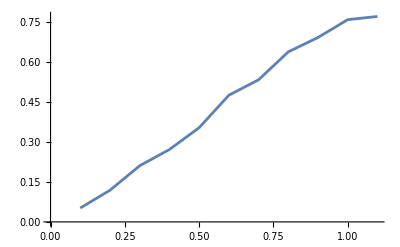

```mathematica
ListPlot[data, Joined->True]
```

## 10. Buffon Needles on Lines

```mathematica
(* Due to symmetry the Buffon needle problem can be constructed as follows. *)
```

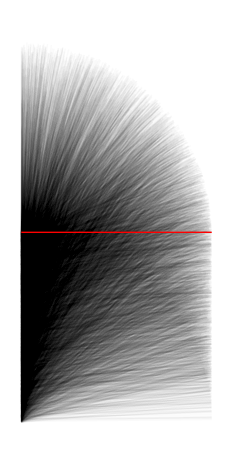
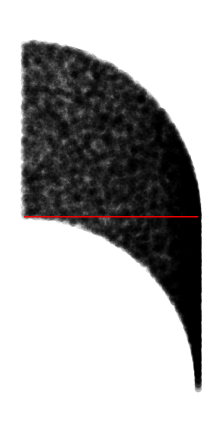

```mathematica
{Graphics[{Opacity[0.02], Line[throwNeedle[1,2]]&/@Range[10000],Opacity[1], Red, Line[{{0,1}, {1,1}}]}], Graphics[{Opacity[0.1],Disk[throwNeedle[1,2][[2]], 0.02]&/@Range[20000], Opacity[1], Red, Line[{{0,1}, {1,1}}]}]}
```

```mathematica
(* These visualizations might help us guess the answer of how many lines end up on the other size of the red line.  The answer appears to be "most of them" but what does that mean?*)
```

```mathematica
N[Length[Select[throwNeedles[1,2, 100000], #[[2]][[2]]>1 &]]/100000]
```

0.63612

```mathematica
N[2/Pi]
```

0.63662

```mathematica
(* Why Pi?  Show derivation.  *)
```

```mathematica
needles={#/10,N[Length[Select[throwNeedles[#/10,2, 5000], #[[2]][[2]]>1 &]]/5000]}&/@Range[200];
```

```mathematica
(* This is how crossing probability relates to the relative length of the needle.  While for L/D = 1, we approach the probability is 0.63 linearly, this value trails off to asymptotically approach 1 for large L/D.

The long time probability the needle doesn't cross is a "power law" INVERSELY proportional to the length.  While the probability on L=D is 2/Pi, the probability for L=10xD is 2/(10*Pi).  One would think there is some weird trigonometry somewhere in here, but I think it simplifies for L >> D
 *)
```

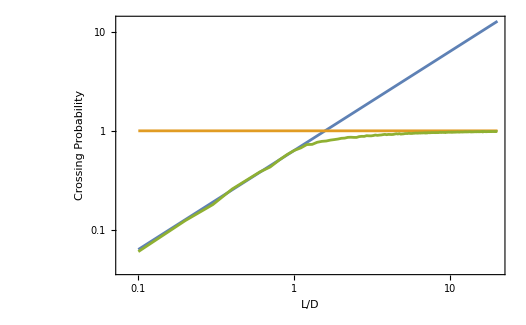

```mathematica
ListLogLogPlot[{{#/10, 2*#/(10*Pi)}&/@Range[200],{#/10, 1}&/@Range[200], needles}, Joined->True, Frame->True, FrameLabel->{"L/D", "Crossing Probability" }]
```

## 11. Needles on Grids (2 D Lines)

```mathematica
results=Table[Table[{N[x/100], N[y/100], computePinPropensity[x/100, y/100]}, {x, 1, 100}], {y,1, 100}];
```

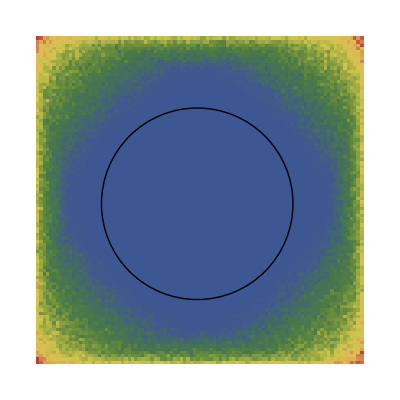

```mathematica
Graphics[{{ColorData["DarkRainbow"][N[#[[3]]]/.25], Rectangle[{#[[1]], #[[2]]}, {#[[1]]+0.01, #[[2]]+0.01}]}&/@Partition[Flatten[results], 3], Black, Circle[{0.5, 0.5}, 1-Sqrt[2]/2]}]
```

```mathematica
(* Two slices of the above grid, one on the edge and one through the equator. *)
```

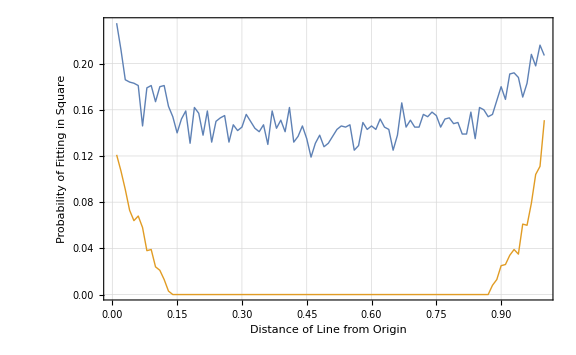

```mathematica
ListPlot[{{#[[1]], #[[3]]}&/@results[[1]], {#[[1]], #[[3]]}&/@results[[50]]}, Joined->True, Frame ->True,FrameStyle->Directive[14], GridLines->Automatic, PlotStyle->Thick, FrameLabel->{"Distance of Line from Origin", "Probability of Fitting in Square"}, ImageSize->Large ]
```

```mathematica
(* What is the maximum distance along the regions equator away from one edge such that it is possible to fit a line of length 1 towards the corner and have it fit.  The is the equivalent of a triangle of hypotenuse 1, one side length 0.5 and the other (1-x).  This translates to solving the following equation. (*Why?) *) *)
```

```mathematica
Solve[x^2 - 2x+0.25==0, x]
```

{{x→0.133975},{x→1.86603}}

```mathematica
(* The corners of the grid should have a value of 0.25, while the halfway point at 0.5 should have a value of 1/6 (~0.17) as the line needs to make at least a 60 degree angle so that it doesn't cross the adjacent side.  But this is not only for points that lie directly on zero but also for points that lie 0.01 off of that value which will dilute (lower) the values a little.
```

## 12. Disks on Grids (The Clean Tile Problem)

```mathematica
data={};
For[i=1,i<1000, i++,
results=pinTileCross[throwCoin[1,i/1000]]&/@Range[100];
data=Append[data,{i/1000,Mean[ Total[#[[1;;2]]]&/@results], Mean[#[[3]]&/@results]}];
]
```

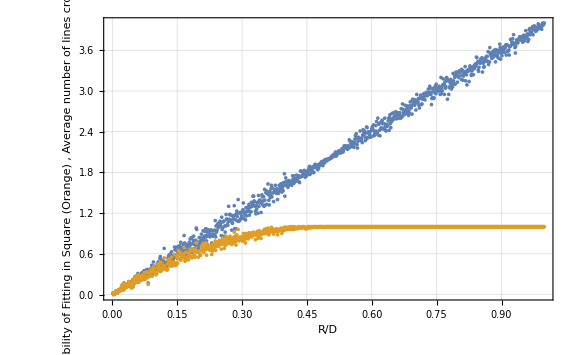

```mathematica
ListPlot[{{#[[1]], #[[2]]}&/@data, {#[[1]], #[[3]]}&/@data}, Frame ->True,FrameStyle->Directive[14], GridLines->Automatic, PlotStyle->Thick, FrameLabel->{"R/D", "Probability of Fitting in Square (Orange) \n, Average number of lines crossed (Blue)"}, ImageSize->Large]
```

```mathematica
(* As the radius approaches half the diamter, the disk must cross a line and is expected to cross 2. *)
```

## 13. Packing (Monodisperse) Disks (In Small Boxes)

```mathematica
(* So far we’ve considered a very short list of things,usually one thing interacting with another.But now we are going to turn up the particle count.There are many directions to go.

What effect does large D/L have?Isolate one boundary->make the other dimension large like a pipe.As the radius of the disks approaches ⅙ the width of the constrained dimension we find another resonance that occurs when two peaks are distinctly clear.As we go above and below this number,the peaks fade away.
 *)
```

```mathematica
YY={0.1+#/100, determineDensity[0.1+#/100, 500]}&/@Range[90];
```

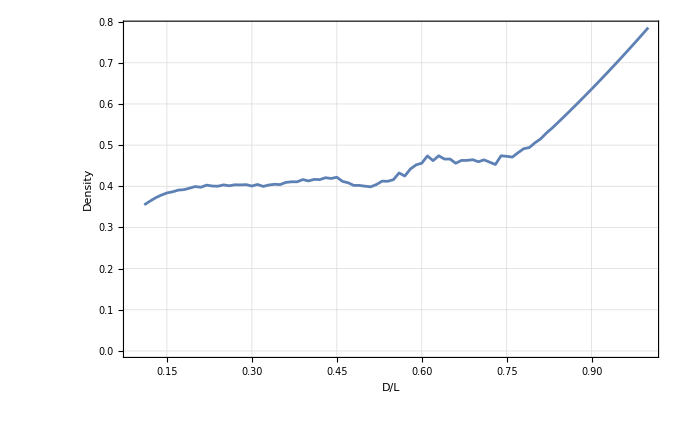

```mathematica
ListPlot[{ {#[[1]], #[[2]]}&/@YY},   Joined->True, PlotRange->All, Frame->True, FrameLabel->{"D/L", "Density"}, GridLines->Automatic, FrameStyle->Directive[14] ]
```

```mathematica
(*  So the right most point here is when the box is as big as the diameter of the box (some ratio of Pi/4.  As the ratio decreases, we are able to fit more than one.  What size box can you add two disks?

Recall this is in two dimensions so there is a chance that you can lay down 2 disks even when L/D is < 2. 

 I think we are seeing the "peaks" at the points when we can fit two disks in the box ((~0.64), 3 points at 0.45 and 4 points at near 0.25


SHOW THIS CALCULATION
```

```mathematica
(* It seems like only when DtoL is <25% are we likely to get more than 1 point in the box. *)
```

```mathematica
XX={0.1+#/10, determineDensity[0.1+#/10, 500]}&/@Range[10]
```

{{0.2,{0.398334,1}},{0.3,{0.402725,1}},{0.4,{0.417032,1}},{0.5,{0.404897,448/499}},{0.6,{0.457829,309/499}},{0.7,{0.449629,84/499}},{0.8,{0.504669,2/499}},{0.9,{0.636173,0}},{1.,{0.785398,0}},{1.1,{0.950332,0}}}

```mathematica
(* This is plotting the probability of more than one disk in the box. Should e be able to fit 2 disks in a box with a D/L of 0.7?  I don't think so! *)
```

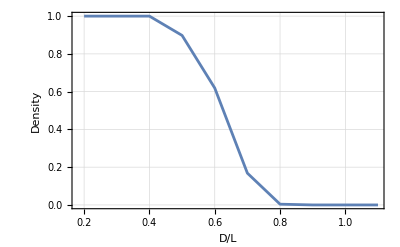

```mathematica
ListPlot[{ {#[[1]], #[[2]][[2]]}&/@XX},   Joined->True, PlotRange->All, Frame->True, FrameLabel->{"D/L", "Probability of More than 1 disk in a box."}, GridLines->Automatic, FrameStyle->Directive[14] ]
```

```mathematica
ZZ={0.01+#/100, determineDensity[0.01+#/100, 10]}&/@Range[20];
```

$Aborted

```mathematica
2+2
```

4

## 14. Monodisperse Disks in Long Rectangles

```mathematica
(* This section considers large aspect ratioregions so we *)
```

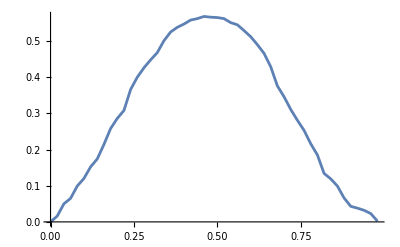

```mathematica
radiusA=0.33;
Q=generateThings2[100, radiusA, 10];
answer33={(#-1)/50, measureSlice[Q,(#-1)/50, radiusA]}&/@Range[50];
{ListPlot[answer33, Joined->True]}
```

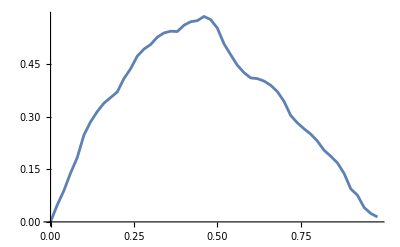

```mathematica
radiusA=0.25;
Q=generateThings2[300, radiusA, 10];
answer25={(#-1)/50, measureSlice[Q,(#-1)/50, radiusA]}&/@Range[50];
ListPlot[answer25, Joined->True]
```

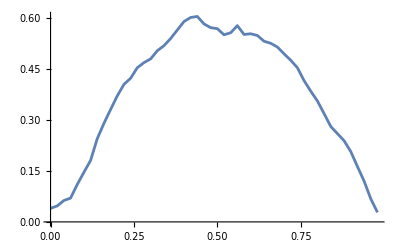

```mathematica
radiusA=0.225;
Q=generateThings2[400, radiusA, 10];
answer225={(#-1)/50, measureSlice[Q,(#-1)/50, radiusA]}&/@Range[50];
ListPlot[answer225, Joined->True]
```

```mathematica
radiusA=0.2;
Q=generateThings2[400, radiusA, 10];
answer2={(#-1)/50, measureSlice[Q,(#-1)/50, radiusA]}&/@Range[50];
```

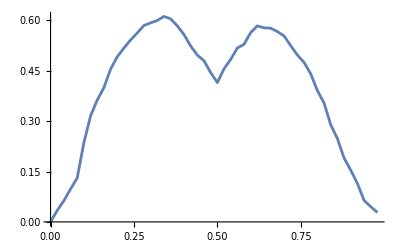

```mathematica
ListPlot[answer2, Joined->True]
```

```mathematica
N[1/6]
```

0.166667

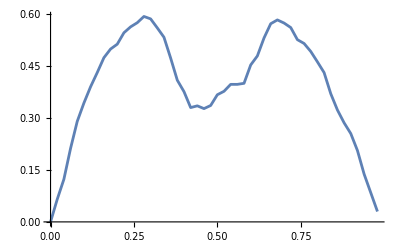

```mathematica
radiusA=0.18;
Q=generateThings2[1000, radiusA, 10];
answer18={(#-1)/50, measureSlice[Q,(#-1)/50, radiusA]}&/@Range[50];
ListPlot[answer18, Joined->True]
```

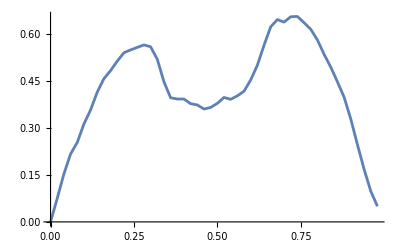

```mathematica
radiusA=0.167;
Q=generateThings2[1000, radiusA, 10];
answer167={(#-1)/50, measureSlice[Q,(#-1)/50, radiusA]}&/@Range[50];
ListPlot[answer167, Joined->True]
```

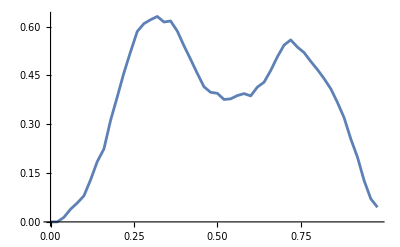

```mathematica
radiusA=1/7;
Q=generateThings2[1000, radiusA, 10];
answer1d7={(#-1)/50, measureSlice[Q,(#-1)/50, radiusA]}&/@Range[50];
ListPlot[answer1d7, Joined->True]
```

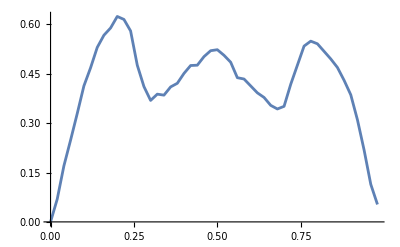

```mathematica
radiusA=0.125;
Q=generateThings2[1000, radiusA, 10];
answer125={(#-1)/50, measureSlice[Q,(#-1)/50, radiusA]}&/@Range[50];
ListPlot[answer125, Joined->True]
```

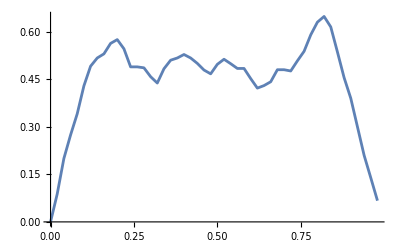

```mathematica
radiusA=0.11;
Q=generateThings2[5000, radiusA, 10];
answer11={(#-1)/50, measureSlice[Q,(#-1)/50, radiusA]}&/@Range[50];
ListPlot[answer11, Joined->True]
```

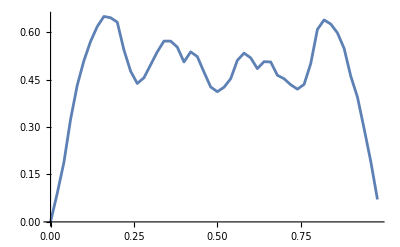

```mathematica
radiusA=0.1;
Q=generateThings2[5000, radiusA, 10];
answer1={(#-1)/50, measureSlice[Q,(#-1)/50, radiusA]}&/@Range[50];
ListPlot[answer1, Joined->True]
```

```mathematica
(* The effect of peaks probably only appear after the *)
```

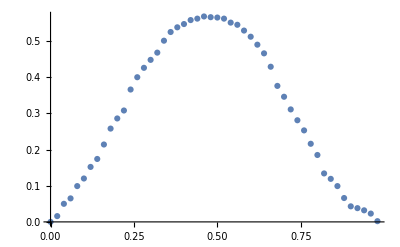
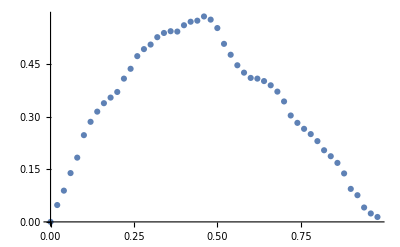
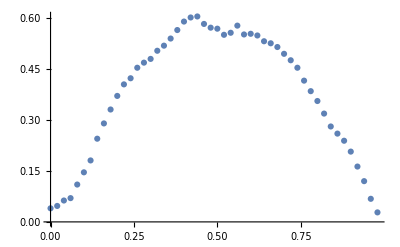
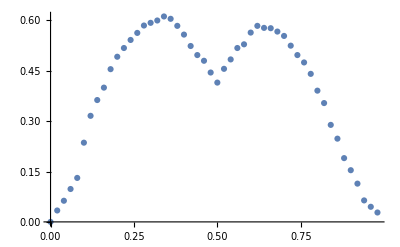
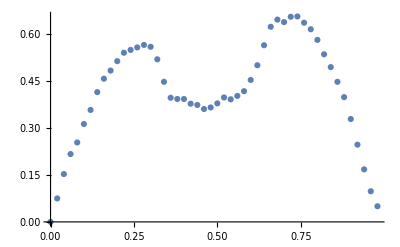
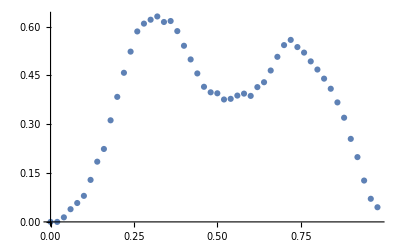
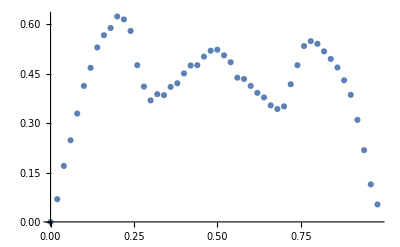
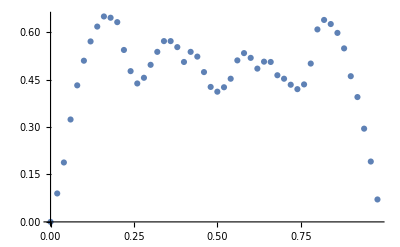

```mathematica
ListPlot[#]&/@{answer33, answer25, answer225, answer2, answer167,answer1d7, answer125,  answer1}
```

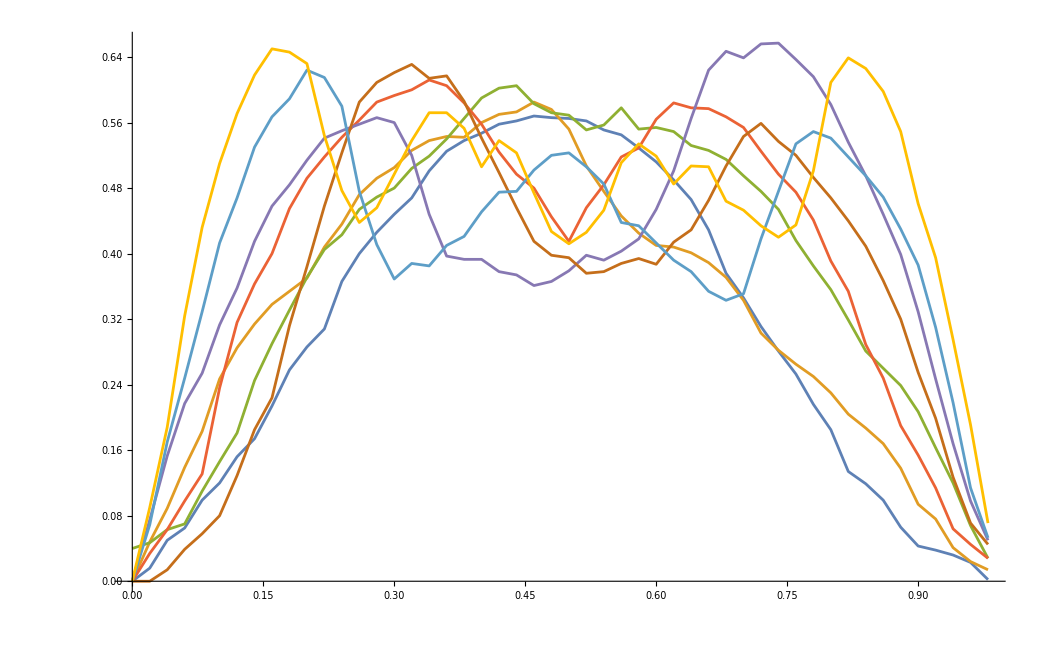

```mathematica
ListPlot[{answer33, answer25, answer225, answer2, answer167,answer1d7, answer125,  answer1} , Joined->True]
```

## 15. Monodisperse, Time for Convergence

```mathematica
result05a=generateThings[10000, 0.05];
result05b=generateThings[10000, 0.05];
result05c=generateThings[10000, 0.05];
result05d=generateThings[10000, 0.05];
```

```mathematica
(* Plotting here the packing fraction compared to the number of iterations.  So for a disk of radius 1/20 the size of the box, it takes about 1/(2*R)^2 to start converging on the answer.  *)
```

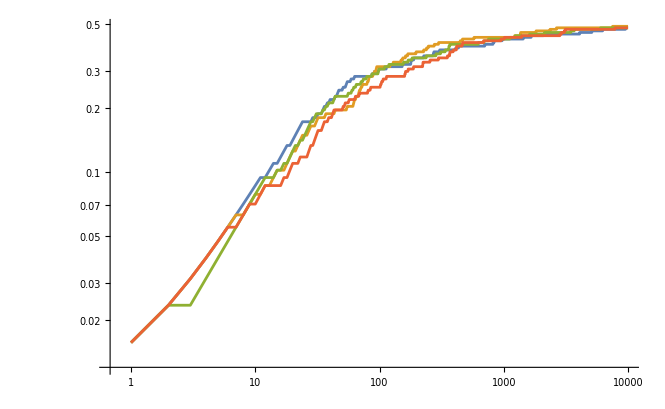

```mathematica
ListLogLogPlot[{{#[[1]], Pi*#[[2]]*0.05^2}&/@result05a[[2]], {#[[1]], Pi*#[[2]]*0.05^2}&/@result05b[[2]], {#[[1]], Pi*#[[2]]*0.05^2}&/@result05c[[2]], {#[[1]], Pi*#[[2]]*0.05^2}&/@result05d[[2]]}, Joined->True, PlotRange->All]
```

```mathematica
result15a=generateThings[10000, 0.15];
result1a=generateThings[10000, 0.1];
result05a=generateThings[10000, 0.05];
result01a=generateThings[10000, 0.01];
```

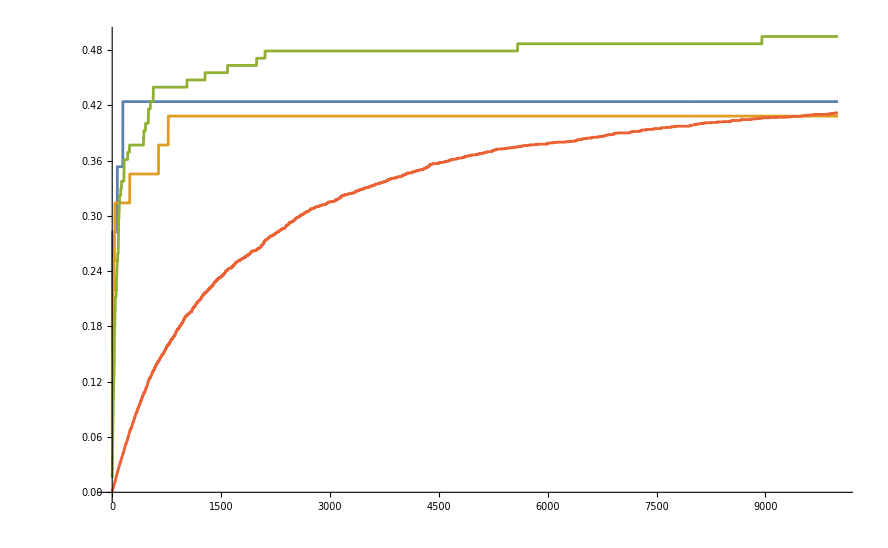

```mathematica
ListPlot[{{#[[1]], Pi*#[[2]]*0.15^2}&/@result15a[[2]], {#[[1]], Pi*#[[2]]*0.1^2}&/@result1a[[2]], {#[[1]], Pi*#[[2]]*0.05^2}&/@result05a[[2]], {#[[1]], Pi*#[[2]]*0.01^2}&/@result01a[[2]]}, Joined->True, PlotRange->All]
```

```mathematica
result07a=generateThings[100000, 0.07];
result06a=generateThings[100000, 0.06];
result04a=generateThings[100000, 0.04];
result03a=generateThings[100000, 0.03];
result02a=generateThings[100000, 0.02];
```

```mathematica
ListLogLogPlot[{{#[[1]], Pi*#[[2]]*0.07^2}&/@result07a[[2]], {#[[1]],Pi*#[[2]]*0.06^2}&/@result06a[[2]], {#[[1]], Pi*#[[2]]*0.04^2}&/@result04a[[2]], {#[[1]], Pi*#[[2]]*0.03^2}&/@result03a[[2]], {#[[1]], Pi*#[[2]]*0.02^2}&/@result02a[[2]]}, Joined->True, PlotRange->All, GridLines->Automatic, Frame->True, FrameLabel->{"iterations", "Coverage by Disks"}]
```

-Graphics-

```mathematica
(* So the *)
```

```mathematica
ListLogLogPlot[{
{ Pi*#[[1]]*0.07^2, Pi*#[[2]]*0.07^2}&/@result07a[[2]], 
{ Pi*#[[1]]0.06^2,Pi*#[[2]]*0.06^2}&/@result06a[[2]], 
{ Pi*#[[1]]*0.04^2, Pi*#[[2]]*0.04^2}&/@result04a[[2]],
 { Pi*#[[1]]*0.03^2, Pi*#[[2]]*0.03^2}&/@result03a[[2]], 
{ Pi*#[[1]]*0.02^2, Pi*#[[2]]*0.02^2}&/@result02a[[2]]}, Joined->True, PlotRange->All, GridLines->Automatic, Frame->True, FrameLabel->{"disk area utilized", "Coverage by Disks"}]
```

-Graphics-

```mathematica
(* These are beautiful curves showsing how fast the answer converges to "steady state" but the answer remains whether steady state is reached.  What might we think when we add two different densities together? *)
```

## 16. Bidispersity and Polydispersity

```mathematica
(* What is most interesting about this section is that you can pack the density alot closer than 1 depending how things evolve.  For example if you are able to fit a "good chunk" of large disks, then the small disks fill in the cracks getting us much higher than 0.5.*)
```

```mathematica
ddd=makeBidispers[10000, 0.1, 0.02, 0.5];
```

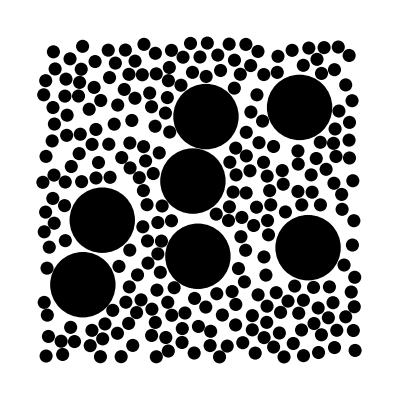

```mathematica
Graphics[Disk[#[[1]], #[[2]]]&/@ddd]
```

```mathematica
Total[Pi*#[[2]]^2&/@ddd]
```

0.546637

```mathematica
eee=makeBidispers[20000, 0.2, 0.02, 0.5]
```

```mathematica
Total[Pi*#[[2]]^2&/@eee]
```

0.585593

```mathematica
fullDataSet=makeBidispers[20000, 0.05+0.3*#/10, 0.02, 0.5]&/@Range[10];
```

```mathematica
Total[Pi*#[[2]]^2&/@fullDataSet[[1]]]
```

0.540354

```mathematica
Total[Pi*#[[2]]^2&/@fullDataSet[[2]]]
```

0.589049

```mathematica
Total[Pi*#[[2]]^2&/@fullDataSet[[3]]]
```

0.58685

```mathematica
Total[Pi*#[[2]]^2&/@fullDataSet[[4]]]
```

0.599102

```mathematica
Total[Pi*#[[2]]^2&/@fullDataSet[[5]]]
```

0.727593

```mathematica
Total[Pi*#[[2]]^2&/@fullDataSet[[6]]]
```

0.553234

```mathematica
Total[Pi*#[[2]]^2&/@fullDataSet[[7]]]
```

0.566743

```mathematica
Total[Pi*#[[2]]^2&/@fullDataSet[[8]]]
```

0.597217

```mathematica
Total[Pi*#[[2]]^2&/@fullDataSet[[9]]]
```

0.623292

```mathematica
Total[Pi*#[[2]]^2&/@fullDataSet[[10]]]
```

0.457416

```mathematica
anotherDataSet=makeBidispers[20000, 0.2, 0.02, 0.5]&/@Range[10];
```

```mathematica
(* Interesting data set, but I bet there is quite a variation for the larger size disks, how many actually appear. *)
```

```mathematica
Total[Pi*#[[2]]^2&/@#]&/@anotherDataSet
```

{0.593133,0.590619,0.522761,0.526531,0.599416,0.69115,0.521504,0.588106,0.643398,0.652195}

```mathematica
Total[Pi*#[[2]]^2&/@eee]
```

```mathematica
ddd[[1]]
```

{{0.742263,0.971593},0.02}

```mathematica
ddd
```

{{{0.646163,0.895624},0.02},{{0.557414,0.114419},0.02},{{0.265597,0.720012},0.1},{{0.284748,0.469389},0.1},{{0.883319,0.483386},0.02},{{0.59932,0.182025},0.02},{{0.0660028,0.753932},0.02},{{0.448001,0.859653},0.1}}

```mathematica
makePolydisperse[num_]:=Module[{i, L, things={{{Random[], Random[]}, Random[]}}, position,radius={},firstRadius,  distances},
firstRadius=0.5*Random[];
position={(1-2*firstRadius)*Random[]+firstRadius, (1-2*firstRadius)*Random[]+firstRadius};
things={{position, firstRadius}};
For[i=1, i<num,
radius=0.5*Random[];
position={(1-2*radius)*Random[]+radius, (1-2*radius)*Random[]+radius};
distances=isOverlapping[{position, radius,  #[[1]], #[[2]]}]&/@things;
L=Total[distances];
things=If[L==0, Append[things,{ position, radius}], things];
i++];
things]
```

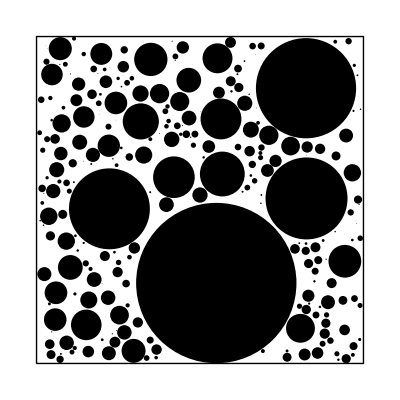

```mathematica
xxx=makePolydisperse[20000];
Graphics[{Disk[#[[1]], #[[2]]]&/@xxx, Line[{{0,0}, {1,0}, {1,1}, {0, 1}, {0,0}}]}]
```

```mathematica
(* There is no reason why we shouldn't be able to fill up all the white space here with black dots as long as we are able to select small dots.  But convergence taking continuous longer for every particle added because 1) more particles and 2) needing to select smaller particles as it get more crowded.  How can we be smarter about that*)
```

```mathematica
Total[Pi*#[[2]]^2&/@xxx]
```

0.602954

## 17. Packing and Percolation

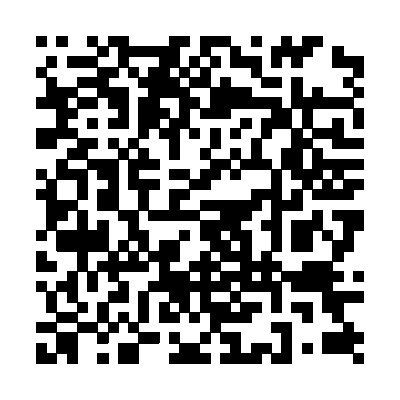

```mathematica
available=fillGrid[33, 500];
Graphics[{Rectangle[#,#+{1,1}]&/@available}]
```

```mathematica
largestPieces={10*#/999,computeLargestPiece[33, 10*#]}&/@Range[90]
```

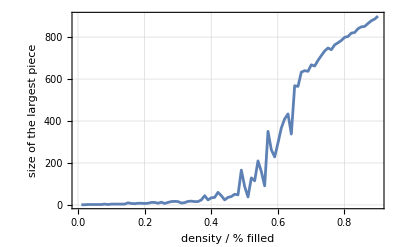

```mathematica
ListPlot[largestPieces, Joined->True, GridLines->Automatic, Frame->True, FrameLabel->{"density / % filled", "size of the largest piece"}]
```

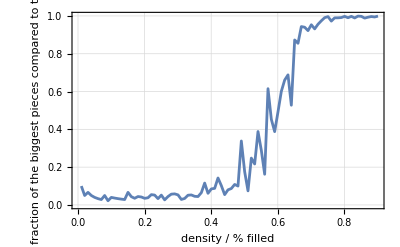

```mathematica
ListPlot[{#[[1]],#[[2]]/(1000*#[[1]])}&/@ largestPieces, Joined->True, GridLines->Automatic, Frame->True, FrameLabel->{"density / % filled", "fraction of the biggest pieces compared to total"}]
```

```mathematica
2+2
```

4